```mathematica
sesh4DetTraces = (Import[#, "Numeric"->True][[1]]&/@ allBinDetFilenames[{4}]);
```

```mathematica
winLength = 3;
```

```mathematica
trainTuples := Flatten[Partition[#, winLength+1] & /@ sesh4DetTraces,1] /. {1 -> True, 0-> False};
features := trainTuples[[All,1;;winLength]]; 
labels := trainTuples[[All,winLength +1]];
```

```mathematica
pred = Classify[features -> labels, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Tally@MapThread[Xor, {pred@features, labels}]
```

{{False,612},{True,73}}

```mathematica
(* Accuracy *) 
N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]
```

0.893431

```mathematica
(* a quick and dirty test for different window sizes *) 
accuracies = With[{winSize = #}, trainTuples := Flatten[Partition[#, winSize+1] & /@ sesh4DetTraces,1] /. {1 -> True, 0-> False};
features := trainTuples[[All,1;;winSize]]; 
labels := trainTuples[[All,winSize+1]];
pred = Classify[features -> labels, Method->"LogisticRegression"];
{#, N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]}
]& /@ Range[1,60]
```

{{1,0.851528},{2,0.861354},{3,0.893431},{4,0.883424},{5,0.890591},{6,0.877238},{7,0.906158},{8,0.888158},{9,0.919708},{10,0.898785},{11,0.911894},{12,0.894737},{13,0.876289},{14,0.895604},{15,0.905882},{16,0.930818},{17,0.88},{18,0.888112},{19,0.919118},{20,0.914063},{21,0.893443},{22,0.915254},{23,0.920354},{24,0.906542},{25,0.903846},{26,0.888889},{27,0.9375},{28,0.836957},{29,0.945055},{30,0.965116},{31,0.940476},{32,0.9},{33,0.987179},{34,0.935065},{35,0.918919},{36,0.972222},{37,0.985714},{38,0.970588},{39,0.940299},{40,0.953846},{41,0.968254},{42,0.83871},{43,0.949153},{44,0.847458},{45,0.931034},{46,1.},{47,0.872727},{48,0.962264},{49,0.961538},{50,1.},{51,0.901961},{52,1.},{53,0.979167},{54,0.978723},{55,0.956522},{56,0.978261},{57,0.866667},{58,0.866667},{59,0.955556},{60,0.904762}}

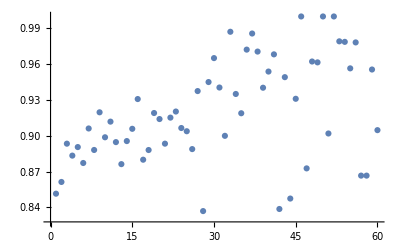

```mathematica
ListPlot[accuracies]
```